#### Requirements

```mathematica
Needs["MaTeX`"]
<<MaTeX`
```

# Momentum spectra

## Importing source files

### Defining paths

```mathematica
path="/Users/jordi/Library/CloudStorage/Box-Box/Research/codes/smash";
export path="/Users/jordi/Library/CloudStorage/Box-Box/Research/codes/smash/output";
```

### Data

#### Experimental data

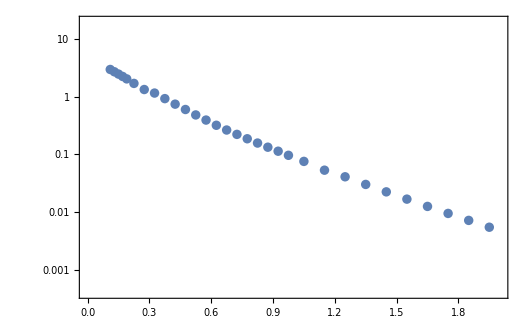

```mathematica
ALICE π 0to5 RawData={
{0.11,0.13,0.15,0.17,0.19,0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{2049.8,2187.3,2291.6,2357.6,2384.7,2356.9,2250.6,2306,2131.4,1937.2,1748.5,1556.7,1382.8,1227.3,1098.9,991.06,890.56,798.43,717.64,646.49,579.66,488.6,376.55,313.76,249.63,199.13,159.51,126.83,102.06,80.97,65.188}
};
ALICE π 5to10 RawData={
{0.11,0.13,0.15,0.17,0.19,0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{1579.6,1723.9,1826.7,1888.3,1920.2,1901,1826.3,1877.9,1735.4,1576.9,1424.6,1265.8,1137,997.44,889.24,803.37,719.99,646.36,580.76,523.34,467.15,395.85,305.53,255.87,203.9,162.97,130.09,103.72,82.765,66.998,53.564}
};
ALICE π 0to10=Table[{ALICE π 0to5 RawData[[1,i]],(ALICE π 0to5 RawData[[2,i]]+ALICE π 5to10 RawData[[2,i]])/2},{i,1,Length@ALICE π 0to5 RawData[[1]]}];
πData=ListLogPlot[ALICE π 0to10/. {pT_,dNdpT_}:>{pT,1/(2π)2/1765 1/pT dNdpT},PlotRange->{{0,2},{4*10^-4,2*10^1}},
Frame->True,
FrameStyle->Directive[Thick,Black,16]]
```

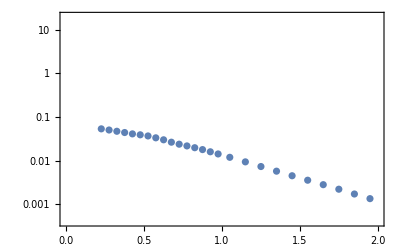

```mathematica
ALICE K 0to5 RawData={
{0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{148.31,168.53,187.27,202.16,213.48,229.8,240.17,238.48,232.7,219.33,212.79,207.8,200.98,193.21,181.89,171.41,153.9,132.73,112.97,95.543,80.706,68.159,57.126,47.442,39.042,32.248}
};
ALICE K 5to10 RawData={
{0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{119.92,139.92,153.77,166.19,175.24,183.96,190.47,188.78,185.8,179.19,172.42,168.2,163.14,156.62,147.57,138.38,125.62,108.19,91.86,77.633,65.481,55.341,46.843,39.387,32.28,26.635}
};
ALICE K 0to10=Table[{ALICE K 0to5 RawData[[1,i]],(ALICE K 0to5 RawData[[2,i]]+ALICE K 5to10 RawData[[2,i]])/2},{i,1,Length@ALICE K 0to5 RawData[[1]]}];
KData=ListLogPlot[ALICE K 0to10/. {pT_,dNdpT_}:>{pT,1/(2π)1/1765 1/pT dNdpT},PlotRange->{{0,2},{4*10^-4,2*10^1}},
Frame->True,
FrameStyle->Directive[Thick,Black,16]]
```

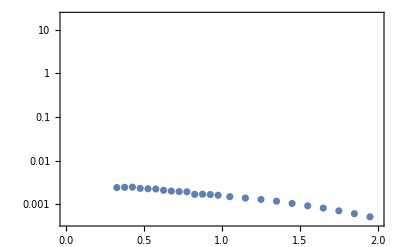

```mathematica
ALICE p 0to5 RawData={
{0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{19.63,22.065,25.729,26.599,29.029,31.572,31.837,33.173,34.681,36.87,34.279,36.002,37.685,38.159,38.122,38.924,39.512,39.003,37.157,35.115,33.309,30.693,28.055,24.843}
};
ALICE p 5to10 RawData={
{0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95},
{15.56,19.042,21.363,22.602,24.463,26.278,26.686,27.697,28.752,30.301,28.279,30.674,31.569,32.286,32.082,32.785,32.77,32.273,30.831,29.094,27.155,25.007,22.587,20.328}
};
ALICE p 0to10=Table[{ALICE p 0to5 RawData[[1,i]],(ALICE p 0to5 RawData[[2,i]]+ALICE p 5to10 RawData[[2,i]])/2},{i,1,Length@ALICE p 0to5 RawData[[1]]}];
pData=ListLogPlot[ALICE p 0to10/. {pT_,dNdpT_}:>{pT,1/(2π)0.5/1765 1/pT dNdpT},PlotRange->{{0,2},{4*10^-4,2*10^1}},
Frame->True,
FrameStyle->Directive[Thick,Black,16]]
```

#### Import function

```mathematica
ImportMomentumSpectrumData[inputFile_]:=
Module[{rawInput,newInput,error},
rawInput=Import[FileNameJoin[{path,inputFile}],"Table"];
(* Trim headers *)
newInput=rawInput[[13;;All]];
(* Transpose to obtain a list of columns *)
newInput=Transpose@newInput;
(* Re-scale second column *)
newInput=newInput/. {pTLow_,pTHigh_,sumw_,sumw2_,sumwx_,sumwx2_,dNdpT_}:>{(pTLow+pTHigh)/2,1/(2π)1/((pTLow+pTHigh)/2)dNdpT};
{newInput[[1]],newInput[[2]]}
]
ImportMomentumSpectrumDataWithoutNormalization[inputFile_]:=
Module[{rawInput,newInput,error},
rawInput=Import[FileNameJoin[{path,inputFile}],"Table"];
(* Trim headers *)
newInput=rawInput[[13;;All]];
(* Transpose to obtain a list of columns *)
newInput=Transpose@newInput;
(* Re-scale second column *)
newInput=newInput/. {pTLow_,pTHigh_,sumw_,sumw2_,sumwx_,sumwx2_,dNdpT_}:>{(pTLow+pTHigh)/2,dNdpT};
{newInput[[1]],newInput[[2]]}
]
```

#### PDG21+ with intermediate decays

```mathematica
pT pi IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["data/7/pi.yoda"];
pT K IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["data/7/K.yoda"];
pT p IntermediateDecays PDG21Plus Data=ImportMomentumSpectrumData["data/7/p.yoda"];

TotalChargedMultiplicity PDG21Plus=(2.326538*10^7)*0.1;(* Mean MultCh x bin width *)
```

#### SMASH with full decays

```mathematica
pT pi FullDecays SMASH Data=ImportMomentumSpectrumData["data/6/pi.yoda"];
pT K FullDecays SMASH Data=ImportMomentumSpectrumData["data/6/K.yoda"];
pT p FullDecays SMASH Data=ImportMomentumSpectrumData["data/6/p.yoda"];

TotalChargedMultiplicity SMASH=(2.364637*10^7)*0.1;
(* Mean MultCh x bin width *)
```

## Plot preparation

```mathematica
ScaleMomentumSpectra[spectrum_,scale_]:=
Module[{totalSpectrum},
totalSpectrum=scale*spectrum[[2]];
{spectrum[[1]],totalSpectrum}
]
```

### Intermediate PDG21+ decays vs. SMASH decays

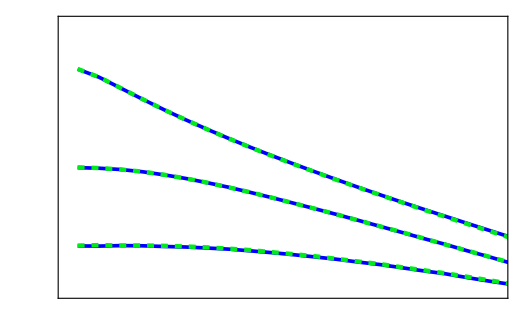
-Graphics--Graphics--Graphics-

```mathematica
PionScale=2;
KaonScale=1;
ProtonScale=0.5;
Nevents=1;
IntermediateDecaysPDG21PlusScale=1/Nevents 1/(TotalChargedMultiplicity PDG21Plus);
SMASHScale=1/Nevents 1/(TotalChargedMultiplicity SMASH);
HadronicRescatteringAndDecaysPlot=ListLogPlot[{
Transpose@ScaleMomentumSpectra[pT pi IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*PionScale],
Transpose@ScaleMomentumSpectra[pT pi FullDecays SMASH Data,1*SMASHScale*PionScale],
Transpose@ScaleMomentumSpectra[pT K IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*KaonScale],
Transpose@ScaleMomentumSpectra[pT K FullDecays SMASH Data,1*SMASHScale*KaonScale],
Transpose@ScaleMomentumSpectra[pT p IntermediateDecays PDG21Plus Data,1*IntermediateDecaysPDG21PlusScale*ProtonScale],
Transpose@ScaleMomentumSpectra[pT p FullDecays SMASH Data,1*SMASHScale*ProtonScale]
},
PlotRange->{{0,2},{4*10^-4,2*10^1}},
Frame->True,
FrameStyle->Directive[Thick,Black,16],
FrameTicks->{
{(* primary Y-axis ticks *)
With[{
minorYTicks=Flatten[Table[{j 10^i,"",{0.006,0}},{i,-4,4,1},{j,2,9}],1],
mayorYTicks={
{10^-4,MaTeX["10^{-4}",Magnification->2],{0.015,0}},
{10^-3,MaTeX["10^{-3}",Magnification->2],{0.015,0}},
{10^-2,MaTeX["10^{-2}",Magnification->2],{0.015,0}},
{10^-1,MaTeX["10^{-1}",Magnification->2],{0.015,0}},
{10^0,MaTeX["1",Magnification->2],{0.015,0}},
{10^1,MaTeX["10",Magnification->2],{0.015,0}},
{10^2,MaTeX["10^{2}",Magnification->2],{0.015,0}},
{10^3,MaTeX["10^{3}",Magnification->2],{0.015,0}},
{10^4,MaTeX["10^{4}",Magnification->2],{0.015,0}}
}},
Join[minorYTicks,mayorYTicks]],
(* secondary Y-axis ticks *)
With[{
minorYTicks=Flatten[Table[{j 10^i,"",{0.006,0}},{i,-5,4,1},{j,2,9}],1],
mayorYTicks=Table[{10^i,"",{0.015,0}},{i,-5,4,1}]},
Join[minorYTicks,mayorYTicks]]},
{(* primary X-axis ticks *)
With[{
minorXTicks=Table[i,{i,0,3,0.1}],
mayorXTicks={0,0.5,1,1.5,2,2.5,3}},
Join[{#,"",{0.006,0}} &/@ minorXTicks,
{#,MaTeX[#,Magnification->2],{0.015,0}} &/@ mayorXTicks]],
(* secondary X-axis ticks *)
With[{
minorXTicks=Table[i,{i,0,3,0.1}],
mayorXTicks=Table[i,{i,0,3,0.5}]},
Join[{#,"",{0.006,0}} &/@ minorXTicks,
{#,"",{0.015,0}} &/@ mayorXTicks]]}},
PlotStyle->{
Directive[Thickness[0.005],Blue],
Directive[Dashed,Thickness[0.006],RGBColor[0, 0.92, 0.11]]
},
ImageSize->128*4.135,
PlotLegends->Placed[LineLegend[
MaTeX[{
"1\\rightarrow2\\ \\text{decays},\\, \\text{PDG2021+} ",
"1\\rightarrow2\\ \\text{decays},\\, \\text{SMASH list}"
},FontSize->20],LegendLayout->{"Column",1},LegendMarkers->"",Spacings->0.2],{0.69,0.75}],
Epilog->{
Text[Style[MaTeX[ToString[PionScale]<>"\\times (\\pi^+ + \\pi^-)",Magnification->2]], Scaled[{0.205,0.87}]],
Text[Style[MaTeX["K^+ + K^-",Magnification->2]], Scaled[{0.15,0.52}]],
Text[Style[MaTeX[ToString[ProtonScale]<>"\\times (p+\\overline{p})",Magnification->2]], Scaled[{0.18,0.265}]],
Text[Style[MaTeX["\\text{BW+SMASH}",FontSize->20]], Scaled[{0.79,0.59}]]
},
Joined->True];
LabeledHadronicRescatteringAndDecaysPlot=Labeled[Show[HadronicRescatteringAndDecaysPlot, Method->{"ShrinkWrap"->True}],MaTeX[{"\\frac{1}{2\\pi N_\\text{ch}}\\,\\frac{dN}{p_T\\hspace{1mm} dp_T}","p_T\; [\\text{GeV}]"},FontSize->24],{Left,Bottom},Spacings->{0,0},RotateLabel->True]
Export[FileNameJoin[{export path,"Fig_SMASH_decays_momentum_spectra.pdf"}],LabeledHadronicRescatteringAndDecaysPlot];
```